Nanometer STM

```mathematica
color = {RGBColor[1, 31/255, 91/255], RGBColor[0, 41/51, 36/85], RGBColor[0, 154/255, 74/85], RGBColor[35/51, 88/255, 62/85],
RGBColor[1, 66/85, 2/17],
RGBColor[242/255, 133/255, 2/15],RGBColor[0, 92/255, 171/255]};Fix[data_]:=Table[If[ i≠ 1&&data⟦i⟧==0&&data⟦i-1⟧≥0.3,data⟦i-1⟧,data⟦i⟧],{i, 1, Length[data]}];
```

```mathematica
(*Feedback*)
MaxsFantasticPlottingFunction[datafile_,picfile_, datapadding_, centercoords_]:=(
ip={{100,100},{60,25}};
th = 0.007;
imgsize = Large;
Export["C:\\Users\\freem\\Documents\\GitHub\\HapticSPM\\Resources\\Plots\\rawvsplot_ticks.png",
plot=Overlay[{
ListPlot[Abs[current],
Joined->True ,
ImagePadding->ip,
ImageSize->imgsize,
PlotStyle->Directive[color⟦1⟧, Thickness[0.01]],
Frame->{True,True,True,False},
FrameStyle->{Directive[Black, Thickness[th]],
Directive[color⟦1⟧, Thickness[th]],Directive[Black, Thickness[th]],Directive[Black, Thickness[th]]},
FrameLabel->{{"STM Tunneling Current (pA)",""},{"Iterations",""}},
FrameTicks->{{All, False},{True, False}},
PlotLabel->"Pen Force and Tunneling Current", PlotLegends->Placed[LineLegend[ {color⟦1⟧, color⟦7⟧},{"STM Tunneling Current (pA)", "Pen Force (N)"}],Bottom]],
 ListPlot[Fix[force],Joined->True, ImageSize->imgsize,PlotStyle->Directive[color⟦7⟧, Thickness[0.01]],ImagePadding->ip,Frame->{False,False,False,True},FrameTicks->{{False,All},{False,False}},FrameStyle->Directive[color⟦7⟧, Thickness[th]], PlotLabel->"", PlotRange->All,FrameLabel->{{"","Pen Force(N)"},{"",""}}]}]];
plot)
```

# Write

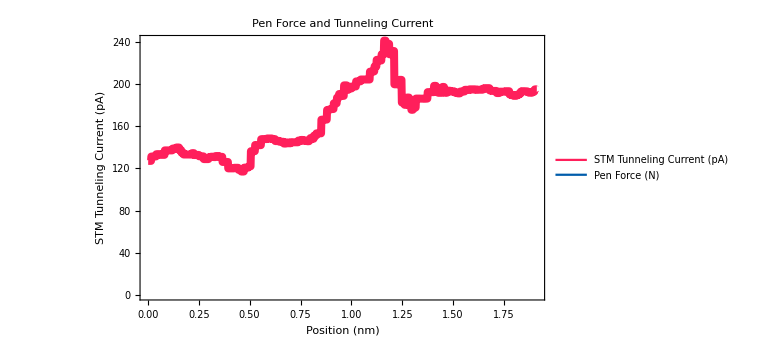
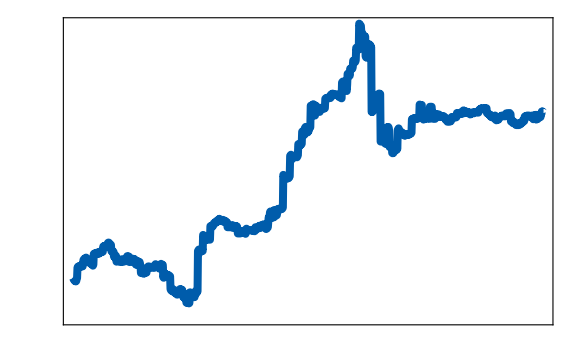

```mathematica
MaxsFantasticPlottingFunction5[datafile_,picfile_, datapadding_, centercoords_]:=(Block[{data,scope,x,y,stmz,current,force,offset, ip, th, imgsize},
data =Transpose[Import[datafile ]];
scope={datapadding⟦1⟧,Length[data⟦1⟧]-datapadding⟦2⟧};
{x,y,stmz,current,force}=data⟦;;,scope⟦1⟧;;scope⟦2⟧⟧;
offset = {centercoords⟦1⟧-3.5,centercoords⟦2⟧-3.5};
ip={{100,100},{60,25}};
th = 0.007;
imgsize = Large;
d = √((x⟦1⟧-x⟦-1⟧)^2+(y⟦1⟧-y⟦-1⟧)^2);
pos =d*Range[Length[x]]/Length[x];

Export["C:\\Users\\freem\\Documents\\GitHub\\HapticSPM\\Resources\\Plots\\rawvsplot_ticks.png",
plot=Overlay[{
ListPlot[Transpose[{pos,Abs[current]}],
Joined->True ,
ImagePadding->ip,
ImageSize->imgsize,
PlotStyle->Directive[color⟦1⟧, Thickness[0.01]],
Frame->{True,True,True,False},
FrameStyle->{Directive[Black, Thickness[th]],
Directive[color⟦1⟧, Thickness[th]],Directive[Black, Thickness[th]],Directive[Black, Thickness[th]]},
FrameLabel->{{"STM Tunneling Current (pA)",""},{"Position (nm)",""}},
FrameTicks->{{All, False},{True, False}},
PlotLabel->"Pen Force and Tunneling Current", PlotLegends->Placed[LineLegend[ {color⟦1⟧, color⟦7⟧},{"STM Tunneling Current (pA)", "Pen Force (N)"}],Bottom]],
 ListPlot[Fix[force],Joined->True, ImageSize->imgsize,PlotStyle->Directive[color⟦7⟧, Thickness[0.01]],ImagePadding->ip,Frame->{False,False,False,True},FrameTicks->{{False,All},{False,False}},FrameStyle->Directive[color⟦7⟧, Thickness[th]], PlotLabel->"", PlotRange->All,FrameLabel->{{"","Pen Force(N)"},{"",""}}]}]];
plot
])
MaxsFantasticPlottingFunction5["C:\\Users\\freem\\Documents\\GitHub\\Backup\\Data\\Raw Z\\Rawz1.csv","C:\\Users\\freem\\Documents\\GitHub\\Plots\\Raw Files\\afm10b.jpg", {3000,0}, {13.03447,-48.96473}]
```